```mathematica
(*This notebook assumes that there is a functional elment experiencing direct selection and is of length l. You can specify various paramters like Ne, mutation rate, recombination rate etc. You can also specify the position as "posn" in base pairs. The notebook will calculate pi at posn, B at posn, and it will plot the recovery of pi from posn=1 to a maximum position (posnmax). Note that you can specify the deleterious DFE as the proportion of mutations belonging to 4 different classes as described in the comments below. If anything is unclear please contact Parul Johri at pjohri1@asu.edu.*)
g = 0; (*rate of gene conversion*)
r = 10^-6 ;(*rate of recombination*)
l = 1000 ;(*Length of genomic element*)
u = 10^-6 ;(*Mutation rate*)
U = l*u;
Ne = 5000 ;(*Effective population size, only required to calculate expected nucleotide diversity under neutrality*)
pi = 4*Ne*u;(*Expected nucleotide diversity under neutrality*)
Clear[y]
f0 = 0.25 ;(*Proportion of effectively neutral mutations with 0 ≤ |2Nes| < 1 *)
f1 = 0.25; (*Proportion of weakly deleterious mutations with 1 ≤ |2Nes| < 10 *)
f2 = 0.25; (*Proportion of moderately deleterious mutations with 10 ≤ |2Nes| < 100 *)
f3 = 0.25 ;(*Proportion of strongly deleterious mutations with |2Nes| >= 100 *)
(*Note that the number of classes can easily be increased to whatever is required to approximate the continuous DFE *)
h = 0.5 ;(* dominance coefficient *)
(*Now we define the boundaries of the fixed intervals over which we will integrate *)
t0 = 0.0;
t1 = h*(1/(2*Ne));
t1half = h*(5/(2*Ne));(* This is the cut-off value of 2Nes=5. This derivation assumes that all mutations with 2Nes<5 will not contribute to BGS *)
t2 = h*(10/(2*Ne));
t3 = h*(100/(2*Ne));
t4 = h*1.0;
posn = 250 ;(* This is the distance (in bp) from the functional element where BGS will be calcualted *)

E14[y_] := (U/(r*l*(1-r y)))*(1 + (r y/((1-r y)*(t4-t3)))*Log[(r y+(1-r y)*t3)/(r y+(1-r y)*t4)]) 
E24[y_] := (-U/(r*l*(1-r(y+l))))*(1+(r(y+l)/((1-r(y+l))*(t4-t3)))*Log[(r(y+l)+(1-r(y+l))*t3)/(r(y+l)+(1-r(y+l))*t4)])

E13[y_] := (U/(r*l*(1-r y)))*(1 + (r y/((1-r y)*(t3-t2)))*Log[(r y+(1-r y)*t2)/(r y+(1-r y)*t3)]) 
E23[y_] := (-U/(r*l*(1-r(y+l))))*(1+(r(y+l)/((1-r(y+l))*(t3-t2)))*Log[(r(y+l)+(1-r(y+l))*t2)/(r(y+l)+(1-r(y+l))*t3)])

E12[y_] := (U/(r*l*(1-r y)))*(1 + (r y/((1-r y)*(t2-t1half)))*Log[(r y+(1-r y)*t1half)/(r y+(1-r y)*t2)]) 
E22[y_] := (-U/(r*l*(1-r(y+l))))*(1+(r(y+l)/((1-r(y+l))*(t2-t1half)))*Log[(r(y+l)+(1-r(y+l))*t1half)/(r(y+l)+(1-r(y+l))*t2)])

(* Calculating pi at posn *)
piB = f0*pi +f1*0.5*pi +f1*0.5*pi*Exp[-1.0*(E12[posn]+E22[posn])] + f2*pi*Exp[-1.0*(E13[posn]+E23[posn])] + f3*pi*Exp[-1.0*(E14[posn]+E24[posn])]
```

0.0181091

```mathematica
(* Calculating B at posn *)
B = piB/pi
```

0.905453

```mathematica
(* Plotting pi astarting at posn 1 (right next to the functional element) and moving to posn_max *)
posnmax = 5000;   (* Specify the maximum value of x-axis *)
```

```mathematica
posn = 0;
piBposn0 = f0*pi +f1*0.5*pi +f1*0.5*pi*Exp[-1.0*(E12[posn]+E22[posn])] + f2*pi*Exp[-1.0*(E13[posn]+E23[posn])] + f3*pi*Exp[-1.0*(E14[posn]+E24[posn])];
```

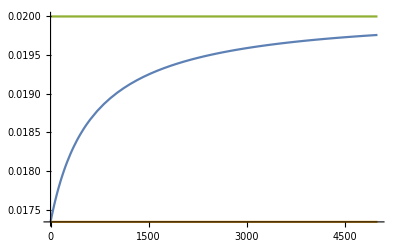

```mathematica
Clear[posn]
piBGS = f0*pi +f1*0.5*pi +f1*0.5*pi*Exp[-1.0*(E12[posn]+E22[posn])] + f2*pi*Exp[-1.0*(E13[posn]+E23[posn])] + f3*pi*Exp[-1.0*(E14[posn]+E24[posn])];
Plot[{piBGS,piBposn0 ,pi}, {posn,0.0, posnmax}]
```